#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documents/MSc_Thesis/3-FEM-Calc/2-Supported-TotallyEmbbeded

Get::noopen: Cannot open ~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls.

$Failed

Get::noopen: Cannot open ~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls.

$Failed

Get::noopen: Cannot open ~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls.

$Failed

Get::noopen: Cannot open ~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls.

$Failed

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
colors
```

{GrayLevel[0],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->"Log",PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->"Log"]},PlotRange->All]&,{{extQ-scaQ,scaQ},Reverse@max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
data = FileNames["1*","Normal"]; data//TableForm

data =Drop[Import[#,"Data"],5]&/@ data;
maxPoints = Array[maxPair[data[[#1,10;;]],1+#2]&,{Length[data],2}] //Transpose;
data = makePairs[data,{2,3}] // Transpose;
```

Normal/1-Efficiency-Embedded-External.csv
Normal/1-Efficiency-Embedded-Internal.csv
Normal/1-Efficiency-Supported-External.csv
Normal/1-Efficiency-Supported-Internal.csv

```mathematica
plots = MapThread[Show[{
ListLogPlot[#1,ImageSize->350,Evaluate[graphsOpts],Joined->True, AspectRatio->1/3.75],
ListLogPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Blue]& @ #2,
#3}]&,{data,maxPoints,Reverse@mie}]
```

{-Graphics-,-Graphics-}

```mathematica
name = "1-Efficiencies"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".pdf"}],#1]&,plots]
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plots]
```

1-Efficiencies

{Normal/1-Efficiencies/1-Efficiencies1.pdf,Normal/1-Efficiencies/1-Efficiencies2.pdf}

{Normal/1-Efficiencies/1-Efficiencies1.svg,Normal/1-Efficiencies/1-Efficiencies2.svg}

Near Field Abs

```mathematica
data =  FileNames["2*","Normal"]
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

{Normal/2-Abs-Near-Embedded-External.csv,Normal/2-Abs-Near-Embedded-Internal.csv,Normal/2-Abs-Near-Supported-External.csv,Normal/2-Abs-Near-Supported-Internal.csv}

Normal/2-Abs-Near-Embedded-External.csv
Normal/2-Abs-Near-Embedded-Internal.csv
Normal/2-Abs-Near-Supported-External.csv
Normal/2-Abs-Near-Supported-Internal.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = {1,-1,1,-1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.55566

{1,-1,1,-1}

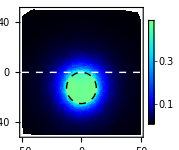
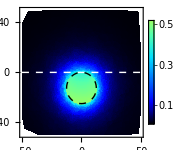
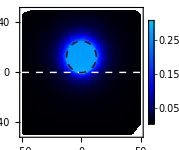
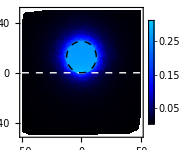

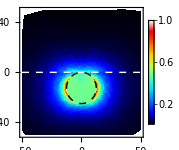
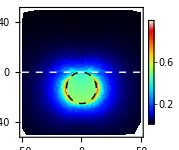
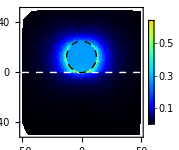
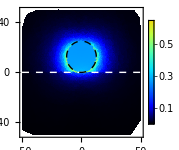

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{-1,-1,1,1};

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Near Field Sca

```mathematica
data =  FileNames["3*","Normal"]
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

{Normal/3-Sca-Near-Embedded-External.csv,Normal/3-Sca-Near-Embedded-Internal.csv,Normal/3-Sca-Near-Supported-External.csv,Normal/3-Sca-Near-Supported-Internal.csv}

Normal/3-Sca-Near-Embedded-External.csv
Normal/3-Sca-Near-Embedded-Internal.csv
Normal/3-Sca-Near-Supported-External.csv
Normal/3-Sca-Near-Supported-Internal.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = {1,-1,1,-1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.90529

{1,-1,1,-1}

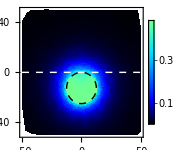
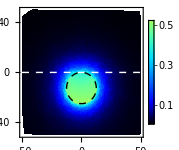
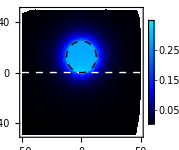
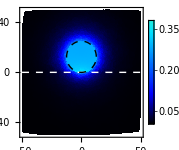

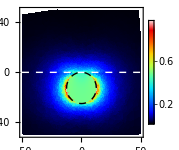
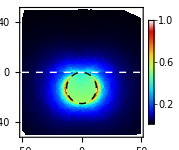
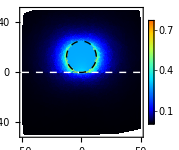
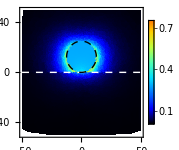

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{-1,-1,1,1};

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Far Field (Normal X, All WaveLengths)

```mathematica
FileNames["4*","Normal"]
```

{Normal/4-5-FarXY,Normal/4-Far-NormalX-Embedded-External.csv,Normal/4-Far-NormalX-Embedded-Internal.csv,Normal/4-Far-NormalX-Supported-External.csv,Normal/4-Far-NormalX-Supported-Internal.csv}

```mathematica
data =  FileNames["4*"~~"*csv","Normal"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
data = Map[Table[#[[i]],{i,1,30,4}]&,data]; (*Choose some wlength*)
```

```mathematica
FileNames["*air*"~~"*txt","Normal"];
wlList=Import[%[[1]],"Data"]//Flatten;
wlList=Table[wlList[[i]],{i,1,30,4}];
name="wl-from-air"
wlList=SwatchLegend[colors[[;;Length[wlList]]],ToString[IntegerPart[#]]<>" nm"&/@wlList]
Export[FileNameJoin[{"Normal","Legends",name<>".svg"}],wlList]
```

wl-from-air

Normal/Legends/wl-from-air.svg

```mathematica
FileNames["*glass*"~~"*txt","Normal"];
wlList=Import[%[[1]],"Data"]//Flatten;
wlList=Table[wlList[[i]],{i,1,30,4}];
name="wl-from-glass"
wlList=SwatchLegend[colors[[;;Length[wlList]]],ToString[IntegerPart[#]]<>" nm"&/@wlList]
Export[FileNameJoin[{"Normal","Legends",name<>".svg"}],wlList]
```

wl-from-glass

Normal/Legends/wl-from-glass.svg

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
caseNP = {-1,-1,1,1}; (*To place above or below the glass*)
caseDir = {-1,1,-1,1}; (*To place the incoming wave direction*)

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[#3*{0,#2}/3.5,#2/3.5]},
Epilog->arrows[Pi/2,#4*#2*1.1]
]&,
{data,max,caseNP,caseDir}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
name = "4-Far-X"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".pdf"}],#1]&,plots]
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plots]
```

4-Far-X

{Normal/4-Far-X/4-Far-X1.pdf,Normal/4-Far-X/4-Far-X2.pdf,Normal/4-Far-X/4-Far-X3.pdf,Normal/4-Far-X/4-Far-X4.pdf}

{Normal/4-Far-X/4-Far-X1.svg,Normal/4-Far-X/4-Far-X2.svg,Normal/4-Far-X/4-Far-X3.svg,Normal/4-Far-X/4-Far-X4.svg}

Far Field (Normal Y, All WaveLengths)

```mathematica
data =  FileNames["5*","Normal"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
data = Map[Table[#[[i]],{i,1,30,4}]&,data]; (*Choose some wlength*)
```

Normal/5-Far-NormalY-Embedded-External.csv
Normal/5-Far-NormalY-Embedded-Internal.csv
Normal/5-Far-NormalY-Supported-External.csv
Normal/5-Far-NormalY-Supported-Internal.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
caseNP = {-1,-1,1,1}; (*To place above or below the glass*)
caseDir = {-1,1,-1,1}; (*To place the incoming wave direction*)

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[#3*{0,#2}/3.5,#2/3.5]},
Epilog->arrows[Pi/2,#4*#2*1.1]
]&,
{data,max,caseNP,caseDir}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
name = "5-Far-Y"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".pdf"}],#1]&,plots]
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plots]
```

5-Far-Y

{Normal/5-Far-Y/5-Far-Y1.pdf,Normal/5-Far-Y/5-Far-Y2.pdf,Normal/5-Far-Y/5-Far-Y3.pdf,Normal/5-Far-Y/5-Far-Y4.pdf}

{Normal/5-Far-Y/5-Far-Y1.svg,Normal/5-Far-Y/5-Far-Y2.svg,Normal/5-Far-Y/5-Far-Y3.svg,Normal/5-Far-Y/5-Far-Y4.svg}